```mathematica
{1,4,5}
```

{1,4,5}

```mathematica
Sin[{Pi/2,Pi,Pi/3,h}]
```

{1,0,(√3)/2,Sin[45]}

```mathematica
SetAttributes[f,Listable]
f[n_] :=Plot[ Cos[x]+ BesselJ[0,x],{x,0,n}]
```

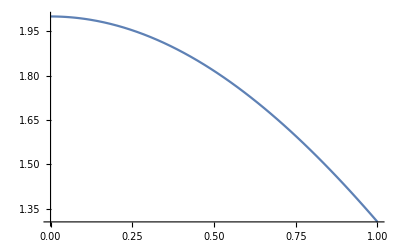
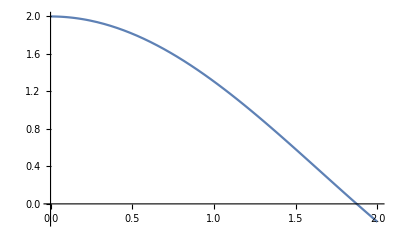
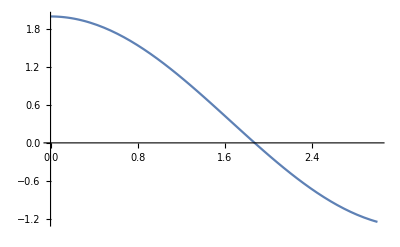
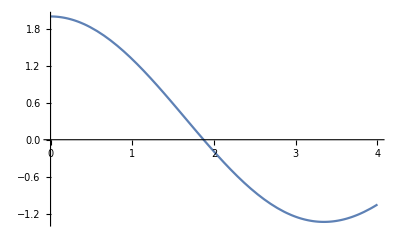
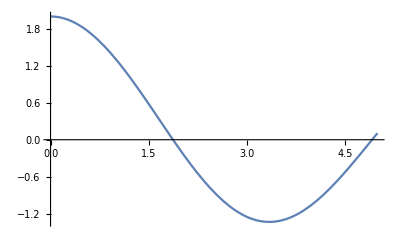
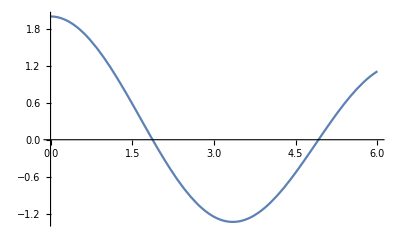
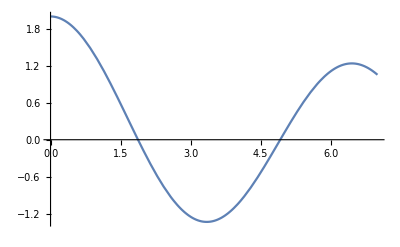
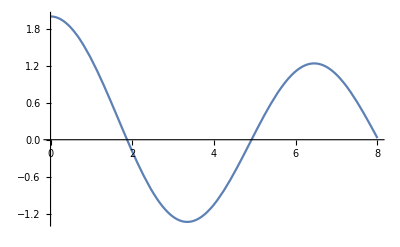

```mathematica
f[Range[50]]
```

```mathematica
g /@ {1,2,3,4}
```

{g[1],g[2],g[3],g[4]}

```mathematica
Map[Framed,{1,2,3}]
```

{1,2,3}

```mathematica
Framed /@ {1,2,3}
```

{1,2,3}

```mathematica
g[x_]:= x^2+1
```

```mathematica
g /@ {1,5/2,6,3,65}
```

{2,29/4,37,10,4226}

```mathematica
ww//@ {a,{b},{c}}
```

ww[{ww[a],ww[{ww[b]}],ww[{ww[c]}]}]

```mathematica
result = Integrate[Cos[x]/(x+1)^5,x]
```

1/24 (((-5+2 x+x^2) Cos[x])/(1+x)^4+Cos[1] CosIntegral[1+x]-((-1+2 x+x^2) Sin[x])/(1+x)^3+Sin[1] SinIntegral[1+x])

## MapAll

```mathematica
MapAll[Framed,result]
```

1/24 Cos[1] CosIntegral[1+x]+Cos[x] -5+2 x+x^2 (1+x)^-4+-1 -1+2 x+x^2 (1+x)^-3 Sin[x]+Sin[1] SinIntegral[1+x]

```mathematica
MapAll[Framed[Labeled[Hyperlink[Head[#], "paclet:ref/" <> ToString[Head[#]]],#]]&,result]
```

Cos[1] CosIntegral[1+x]+Cos[x] -5+x^2+2 x (1+x)^-4+-1 -1+x^2+2 x (1+x)^-3 Sin[x]+Sin[1] SinIntegral[1+x] 1/24

## MapThread

```mathematica
MapThread[ww,{{a,b,c},{1,2,3}}]
```

{ww[a,1],ww[b,2],ww[c,3]}

#### Эквивалент Total

```mathematica
MapThread[Plus,{{a,b,c},{u,v,ww},{x,y,z}}]
```

{a+u+x,b+v+y,40+c+z}

```mathematica
Total[{{a,b,c},{u,v,ww},{x,y,z}}]
```

{a+u+x,b+v+y,c+ww+z}

#### Эквивалент Transpose

```mathematica
MapThread[List, {{a,b,c},{u,v,ww},{x,y,z}}]
```

{{a,u,x},{b,v,y},{c,ww,z}}

```mathematica
Transpose[{{a,b,c},{u,v,ww},{x,y,z}}]
```

{{a,u,x},{b,v,y},{c,ww,z}}

#### Работа с производной

```mathematica
MapThread[D, {{x^5,y+Cos[x],Cos[z+x]/x},{{x,2},y,{{x,y,z}}}}]
```

{20 x^3,1,{-Cos[x+z]/x^2-Sin[x+z]/x,0,-Sin[x+z]/x}}

## MapIndexed

```mathematica
MapIndexed[ww,{a,b,{c}}]
```

{ww[a,{1}],ww[b,{2}],ww[{c},{3}]}

```mathematica
MapIndexed[ww,{a,b,{c}},2]
```

{ww[a,{1}],ww[b,{2}],ww[{ww[c,{3,1}]},{3}]}

```mathematica
MapIndexed[ww,{a,b,{c}},Infinity]
```

{ww[a,{1}],ww[b,{2}],ww[{ww[c,{3,1}]},{3}]}

```mathematica
MapIndexed[ww,Cos[x]+1/x]
```

ww[1/x,{1}]+ww[Cos[x],{2}]

```mathematica
(Cos[x]+1/x)[[2]]
```

Cos[x]

```mathematica
Clear["Global`*"]
```

```mathematica
val={a,{b,{f,{f}}},{{c}},{d,f},g};
```

```mathematica
MapIndexed[Grid[{{#1},{#2}},Frame->All]&,val,{0,Infinity}]
```

{a
{1},{b
{2,1},{f
{2,2,1},{f
{2,2,2,1}}
{2,2,2}}
{2,2}}
{2},{{c
{3,1,1}}
{3,1}}
{3},{d
{4,1},f
{4,2}}
{4},g
{5}}
{}

```mathematica
val[[2,2,2,1]]
```

f

## Apply

#### Замена головной части на другую функцию

```mathematica
f@@g[x]
```

f[x]

```mathematica
Cos@@Sin[x]
```

Cos[x]

```mathematica
ww@@{a,b,c}
```

ww[a,b,c]

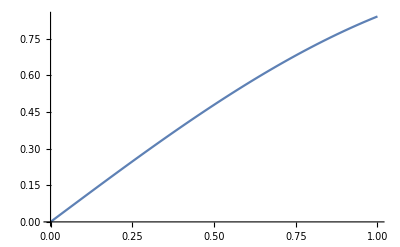
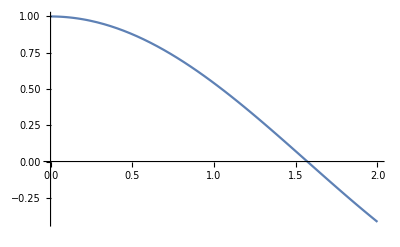
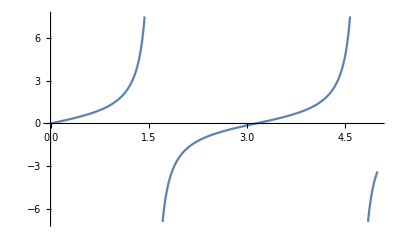

```mathematica
(Plot@@#)&/@{{Sin[x],{x,0,1}},{Cos[x],{x,0,2}},{Tan[x],{x,0,5}}}
```

```mathematica
ww@@@g[{a,v,b}]
```

g[ww[a,v,b]]